# Biomatematika feladatsor 1. gyakorlat

## Elemi feladatok

## Egyenes egyenlete

y = a x + b		y = a (x-x_1) + y_1

### 1. Adja meg az adott (x1, y1) ponton a meredekséggel áthaladó egyenes egyenletét, és határozza meg az x - és y - tengelymetszeteit, majd ábrázolja az egyenest (és a feladatban szereplő pontokat is)

#### (x1, y1) = (0, 0) a = 2

```mathematica
f[x_]=x
```

x

```mathematica
g[x_]=2x
```

2 x

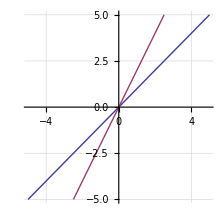

```mathematica
Plot[{f[x],g[x]},{x,-5,5},GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick,PlotRange->5,AspectRatio->Automatic]
```

#### (x1, y1) = (4,0) a = 3

```mathematica
f[x_]=x
```

x

```mathematica
g[x_]=3(x-4)
```

3 (-4+x)

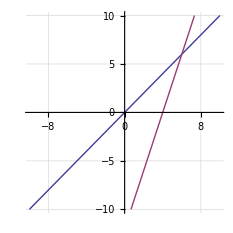

```mathematica
Plot[{f[x],g[x]},{x,-10,10},GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick,PlotRange->10,AspectRatio->Automatic]
```

#### (x1, y1) = (0, 1) a = -2

```mathematica
f[x_]=x
```

x

```mathematica
g[x_]=-2x+1
```

1-2 x

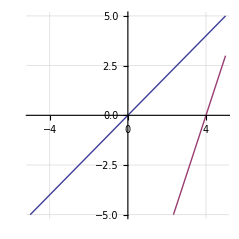

```mathematica
Plot[{f[x],g[x]},{x,-5,5},GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick,PlotRange->5,AspectRatio->Automatic]
```

#### (x1, y1) = (-3, 2) a = -1/2

```mathematica
f[x_]=x
```

x

```mathematica
g[x_]=-0.5(x+3)+2
```

2-0.5 (3+x)

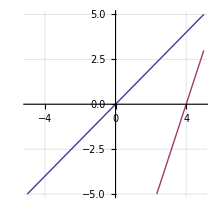

```mathematica
Plot[{f[x],g[x]},{x,-5,5},GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick,PlotRange->5,AspectRatio->Automatic]
```

## Parabola egyenletei

Kanonikus: 	y = a x^2 + b x + c
Csúcsponti: 	y=a (x-p)^2+q
Gyöktényezős: y=a (x-x_1)(x-x_2)

### 2. Határozza meg az alábbi parabola csúcsponti egyenletét és - ha létezik - gyöktényezős egyenletét, és a nevezetes pontjait (x - és y - tengelymetszet, csúcspont koordinátái), és készítsen ábrát!

#### y=x^2-4 x+3

```mathematica
f[x_]=x^2-4x+3
```

3-4 x+x^2

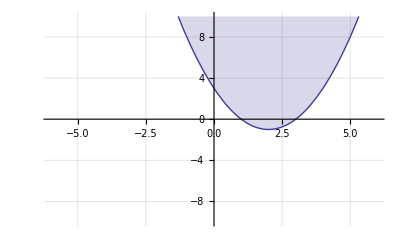

```mathematica
Plot[f[x],{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Filling->Top]
```

## Függvénytranszformációk

## A függő változó (y) transzformációi

### eltolás a függőleges tengelyen

y = f (x) → y = f (x) + d transzformáció : függőleges eltolás 
(d > 0 : fölfelé, d < 0 : lefelé) :

#### y = x^2 + 2

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=x^2+2
```

2+x^2

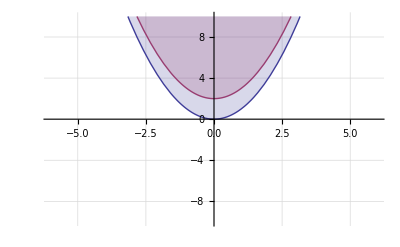

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Filling->Top]
```

#### y = x^3 – 3

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=x^3-3
```

-3+x^3

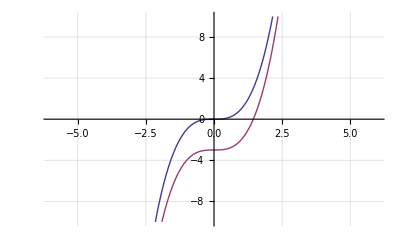

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=√x+6

```mathematica
f[x_]=√x
```

√x

```mathematica
g[x_]=√x+6
```

6+√x

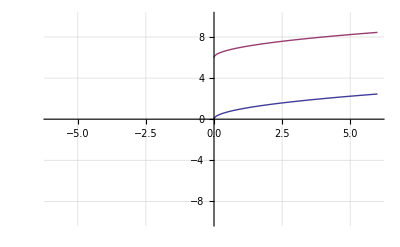

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = 2^x-5

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=2^x-5
```

-5+2^x

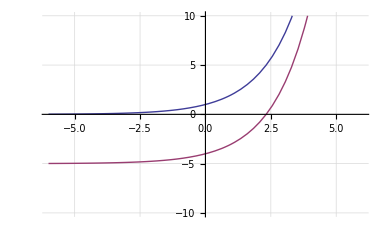

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=Log[x]+5

```mathematica
f[x_]=Log[x]
```

Log[x]

```mathematica
g[x_]=Log[x]+5
```

5+Log[x]

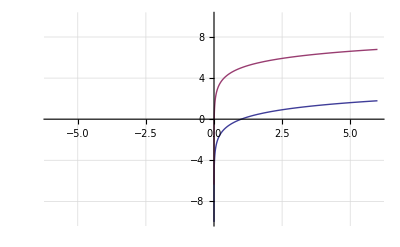

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

### nyújtás a függőleges tengelyen

y = f (x) → y = c f (x), c > 0 transzformáció : függőleges nyújtás 
(c > 1) vagy zsugorítás (c < 1) :

#### y = 2 x^2

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=2(x^2)
```

2 x^2

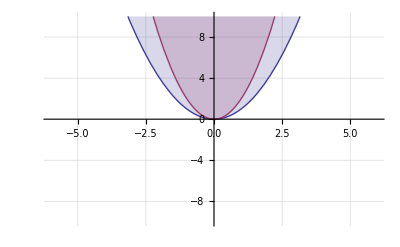

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Filling->Top]
```

#### y = 5 x^3

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=5 x^3
```

5 x^3

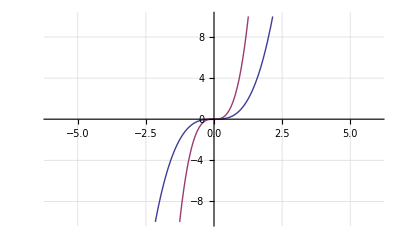

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=6 √x

```mathematica
f[x_]=√x
```

√x

```mathematica
g[x_]=6 √x
```

6 √x

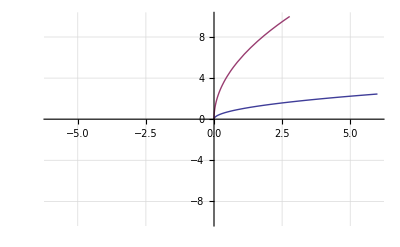

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = 10 2^x

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=10 2^x
```

5 2^(1+x)

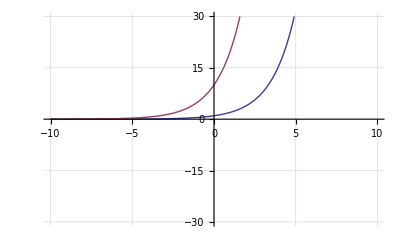

```mathematica
Plot[{f[x],g[x]},{x,-10,10},PlotRange->30,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y= 9 Log[x]

```mathematica
f[x_]=Log[x]
```

Log[x]

```mathematica
g[x_]=9Log[x]
```

9 Log[x]

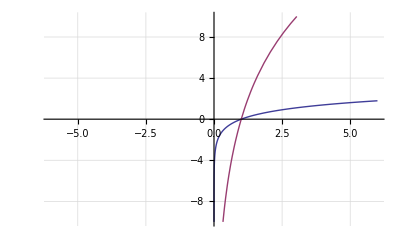

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

### tükrözés a függőleges tengelyre

y = f(x) → y = –f(x) transzformáció: tükrözés az x-tengelyre:

#### y = -x^2

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=-x^2
```

-x^2

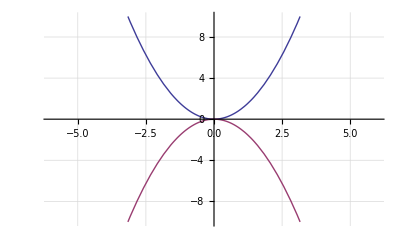

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = -x^3

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=-x^3
```

-x^3

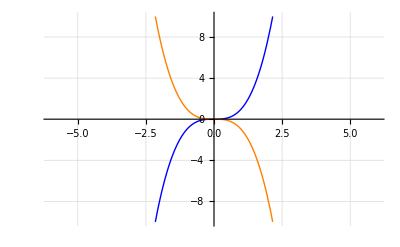

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->{{Thick,Blue},{Thick,Orange}}]
```

#### y=-√x

```mathematica
f[x_]=√x
```

√x

```mathematica
g[x_]=-√x
```

-√x

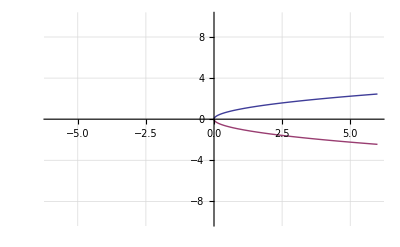

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = -2^x

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=-2^x
```

-2^x

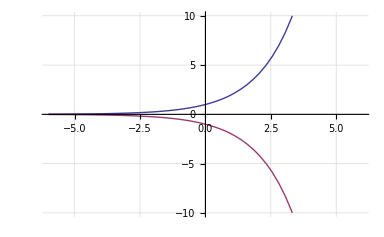

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=Log[x]+5

```mathematica
f[x_]=Log[x]
```

Log[x]

```mathematica
g[x_]=-Log[x]
```

-Log[x]

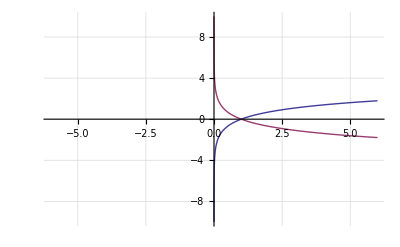

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

## A független változó (x) transzformációi

### eltolás a vízszintes tengelyen

y = f(x) → y = f(x+b) transzformáció: vízszintes eltolás 
(b>0: balra, b<0: jobbra):

#### y = (x+ 2)^2

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=(x+2)^2
```

(2+x)^2

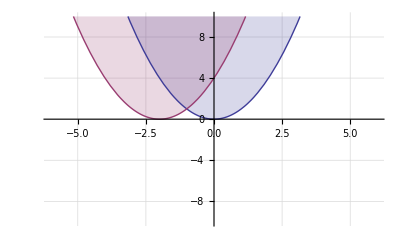

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Filling->Top]
```

#### y =(x-3)^3

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=(x-3)^3
```

(-3+x)^3

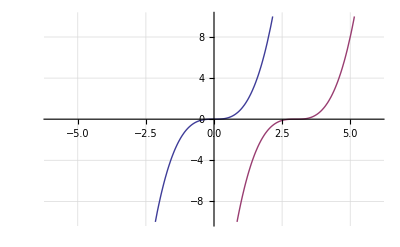

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=√(x+6)

```mathematica
f[x_]=√x
```

√x

```mathematica
g[x_]=√(x+6)
```

√(6+x)

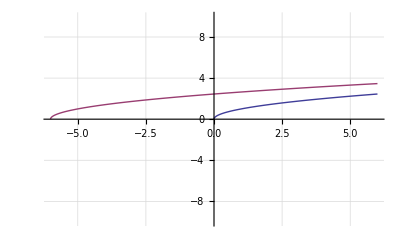

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y =(2-5)^x

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=(2+5)^x
```

7^x

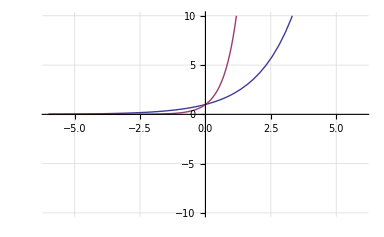

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=Log[x+5]

```mathematica
f[x_]=Log[10,x]
```

Log[x]/Log[10]

```mathematica
g[x_]=Log[10,x+5]
```

Log[5+x]/Log[10]

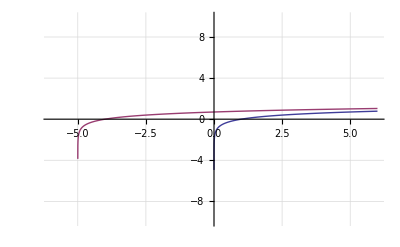

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

### nyújtás a vízszintes tengelyen

y = f(x) → y = c f(x) , c>0 transzformáció: 
függőleges nyújtás (c>1) vagy zsugorítás (c<1):

#### y = (x/2)^2

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=(x/2)^2
```

x^2/4

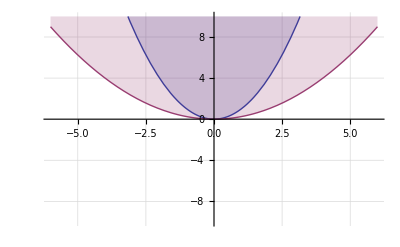

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Filling->Top]
```

#### y =(3 x)^3

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=(3x)^3
```

27 x^3

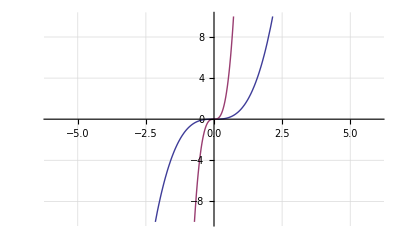

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=√(6x)

```mathematica
f[x_]=√x
```

√x

```mathematica
g[x_]=√(6x)
```

√6 √x

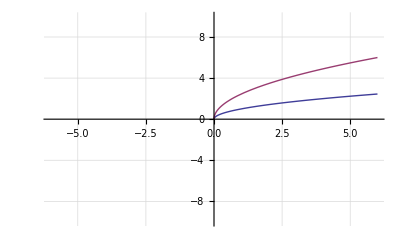

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y =(2/5)^x

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=(5 2)^x
```

10^x

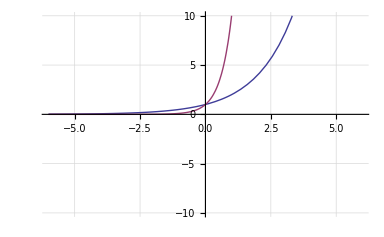

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=Log[30 x]

```mathematica
f[x_]=Log[10,x]
```

Log[x]/Log[10]

```mathematica
g[x_]=Log[10,30x]
```

Log[30 x]/Log[10]

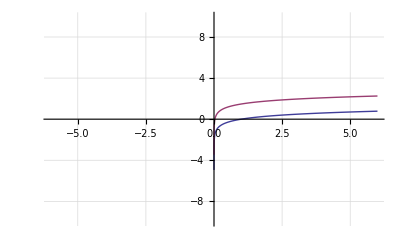

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

### tükrözés a függőleges tengelyre

y = f(x) → y = –f(x) transzformáció: tükrözés az x-tengelyre:

#### y = (-x)^2

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=(-x)^2
```

x^2

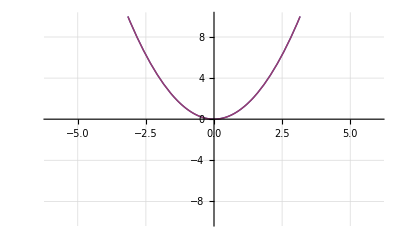

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = (-x)^3

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=(-x)^3
```

-x^3

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->{{Thick,Blue},{Thick,Orange}}]
```

-Graphics-

#### y=√-x

```mathematica
f[x_]=√x
```

√x

```mathematica
g[x_]=√-x
```

√-x

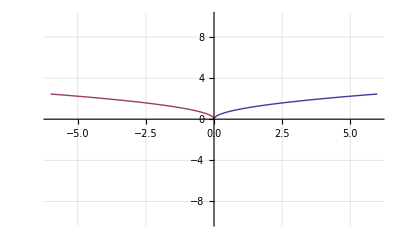

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = (-2)^x

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=(-2)^x
```

(-2)^x

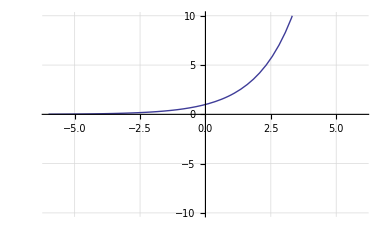

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=Log[-x]

```mathematica
f[x_]=Log[10,x]
```

Log[x]/Log[10]

```mathematica
g[x_]=Log[10,-x]
```

Log[-x]/Log[10]

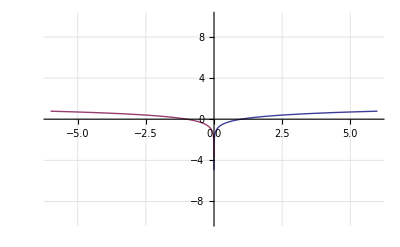

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

## Összetett transzformációk

#### y = –2(x+1)^2+4

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=-2(x+1)^2+4
```

4-2 (1+x)^2

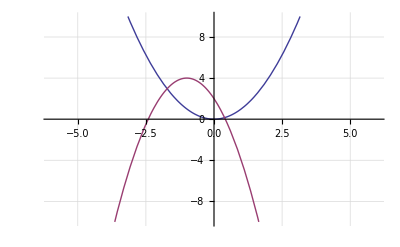

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = 4+2^(-x-2)

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=4+2^(-x-2)
```

4+2^(-2-x)

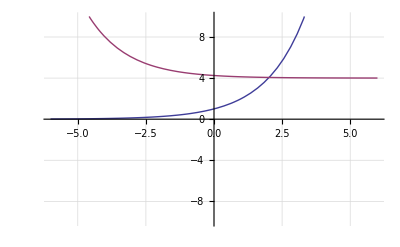

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

## Függvények inverzei

Egy f invertálható valós-valós függvény inverzének grafikonját megkapjuk, ha az y = x egyenletű egyenesre tükrözzük az f grafikonját.

#### y = x^2

```mathematica
f[x_]=x^2
```

x^2

```mathematica
g[x_]=InverseFunction[f][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-√x

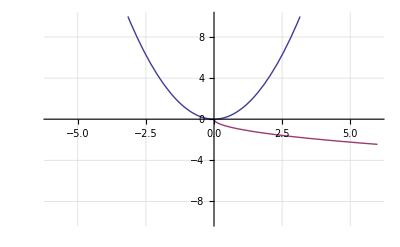

```mathematica
Plot[{f[x],g[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = x^3

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=InverseFunction[f][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

x^(1/3)

```mathematica
h[x_]=x
```

x

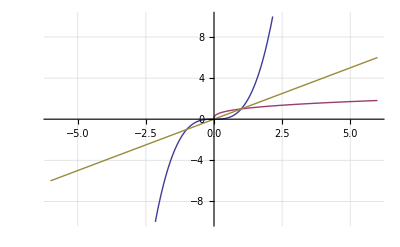

```mathematica
Plot[{f[x],g[x],h[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=√x

```mathematica
f[x_]=√x
```

√x

```mathematica
g[x_]=InverseFunction[f][x]
```

x^2

```mathematica
h[x_]=x
```

x

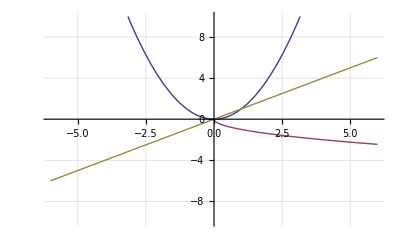

```mathematica
Plot[{f[x],g[x],h[x]},{x,-6,6},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y = 2^x

```mathematica
f[x_]=2^x
```

2^x

```mathematica
g[x_]=InverseFunction[f][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Log[x]/Log[2]

```mathematica
h[x_]=x
```

x

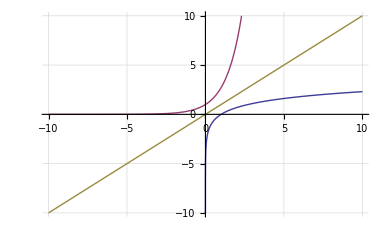

```mathematica
Plot[{f[x],g[x],h[x]},{x,-10,10},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

#### y=Log[x]

```mathematica
f[x_]=Log[x]
```

Log[x]

```mathematica
g[x_]=InverseFunction[f][x]
```

ⅇ^x

```mathematica
h[x_]=x
```

x

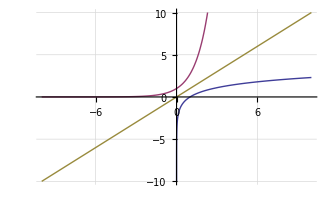

```mathematica
Plot[{f[x],g[x],h[x]},{x,-10,10},PlotRange->10,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],PlotStyle->Thick]
```

## Logaritmikus transzformációk

## Lin-Log (x,y) →( x , log(y) )

b 10^(a x)

#### 10^x

```mathematica
f[x_]=10^x
```

10^x

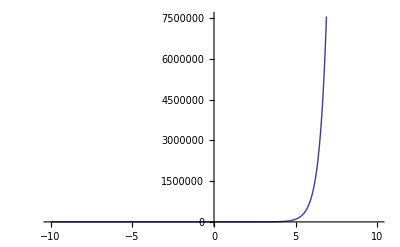

```mathematica
Plot[f[x],{x,-10,10}]
```

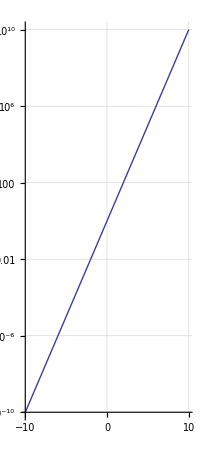

```mathematica
LogPlot[f[x],{x,-10,10},GridLines->Automatic,AspectRatio->Automatic]
```

#### 6 10^(5 x+1)

```mathematica
f[x_]=6 10^(-0.5x+1)
```

3 2^(2-0.5 x) 5^(1-0.5 x)

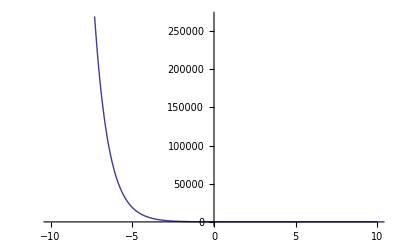

```mathematica
Plot[f[x],{x,-10,10}]
```

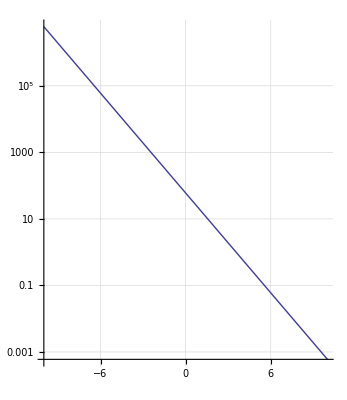

```mathematica
LogPlot[f[x],{x,-10,10},GridLines->Automatic,AspectRatio->Automatic]
```

## Log-Lin (x,y) →( log(x) , y )

b lg(x)+a

#### log[x]

```mathematica
f[x_]=Log[10,x]
```

Log[x]/Log[10]

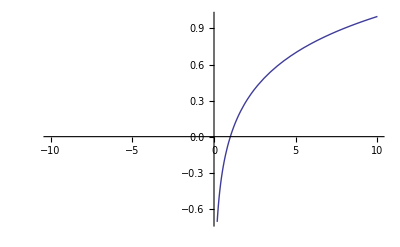

```mathematica
Plot[f[x],{x,-10,10}]
```

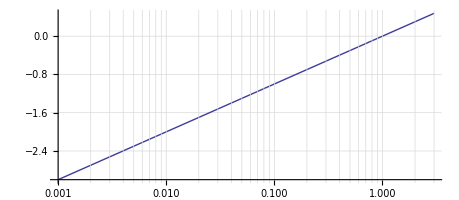

```mathematica
LogLinearPlot[f[x],{x,0.001,3},GridLines->Automatic,AspectRatio->Automatic]
```

#### 2 log[x] + 5

```mathematica
f[x_]=2Log[10,x]+5
```

5+(2 Log[x])/Log[10]

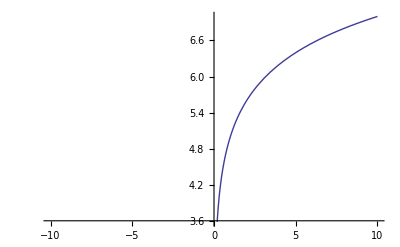

```mathematica
Plot[f[x],{x,-10,10}]
```

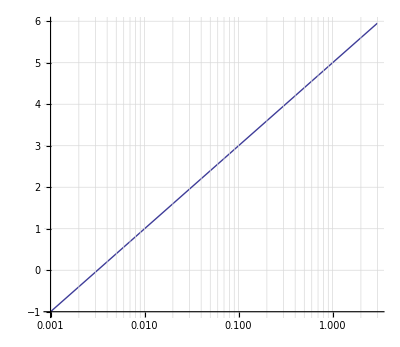

```mathematica
LogLinearPlot[f[x],{x,0.001,3},GridLines->Automatic,AspectRatio->Automatic]
```

## Log-Log (x,y) →( log(x) , log(y) )

b x^k

#### x^3

```mathematica
f[x_]=x^3
```

x^3

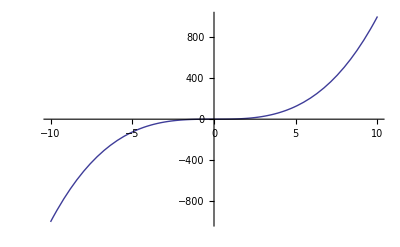

```mathematica
Plot[f[x], {x, -10, 10}]
```

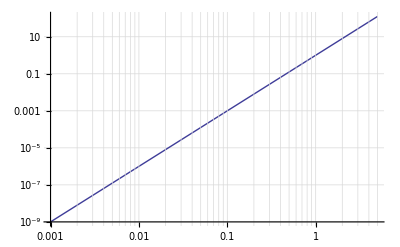

```mathematica
LogLogPlot[f[x],{x,0.001,5},GridLines->Automatic,PlotRange->10]
```

#### 10 x^2

```mathematica
f[x_]=10 x^2
```

10 x^2

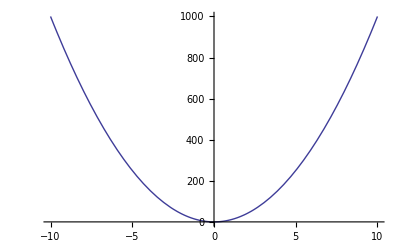

```mathematica
Plot[f[x], {x, -10, 10}]
```

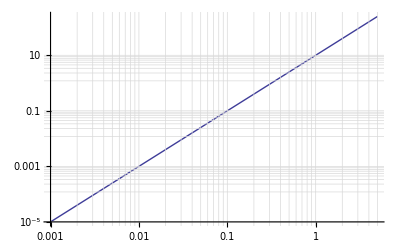

```mathematica
LogLogPlot[f[x],{x,0.001,5},GridLines->Automatic,PlotRange->All]
```